```mathematica
mp=0.938272;
mn=0.939565;
```

```mathematica
μ=(mn+mp)/2;
```

```mathematica
sNN=200;
```

```mathematica
y[en_,m_]:=ArcTanh[(√(en^2-m^2))/en]
```

```mathematica
ρ[r_,θ_,R_,b_,θb_,pm_]:=2/(4/3 π R^3)√(R^2-(r^2+b^2/4+pm r b/2 Cos[θ-θb]))HeavisideTheta[R^2-(r^2+b^2/4+pm r b/2 Cos[θ-θb])];
```

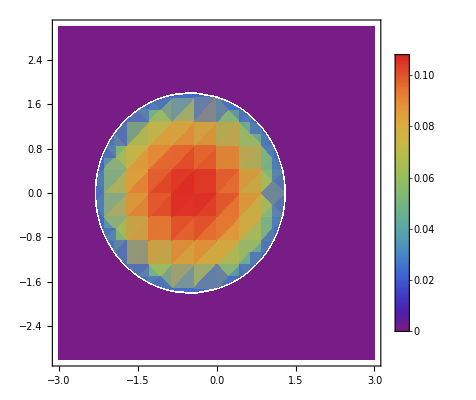

```mathematica
DensityPlot[Evaluate@TransformedField["Polar"->"Cartesian",ρ[r,θ,2,2,0,+1],{r,θ}->{x,y}],{x,-3,3},{y,-3,3},ColorFunction->"Rainbow",PlotLegends->Automatic](*centres at +/- b/2,pm gives different nucleus,R cut off*)
```

```mathematica
Integrate[r ρ[r,θ,R,0,0,+1],{r,0,∞},{θ,0,2π}]
```

ConditionalExpression[((R^2)^(3/2) HeavisideTheta[R^2])/R^3,Im[R]≠0]

```mathematica
τ[t_,z_]:=(t^2-z^2)^(1/2);
η[t_,z_]:=1/2 Log[(t+z)/(t-z)]
```

```mathematica
α=1/137;
Z=83;
```

```mathematica
Bspec[r_,θ_,R_,b_,θb_,pm_,t_,z_,sNN_,m_]:=pm Z α Sinh[y[sNN/2,m]+ pm η[t,z]]NIntegrate[r1 ρ[r1,θ1,R,b,θb,pm](1-HeavisideTheta[R^2-(r1^2+b^2/4+pm r1 b/2 Cos[θ1-θb])])Cross[{r1 Cos[θ1]-r Cos[θ],r1 Sin[θ1]-r Sin[θ],0},{0,0,1}]/((Norm[{r1 Cos[θ1]-r Cos[θ],r1 Sin[θ1]-r Sin[θ]}]^2+τ[t,z]^2 Sinh[y[sNN/2,m]- pm η[t,z]]^2)^(3/2)),{r1,0,10},{θ1,0,2π}]
```

```mathematica
ρ[0,0,7,4,0,+1]
```

(9 √5)/(686 π)

```mathematica
Bspec[0,0,7,4,0,+1,1,1,sNN,μ]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,10},{0,6.28319}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

{∞ NIntegrate[Indeterminate,{r1,0,10},{θ1,0,2 π}],∞ NIntegrate[Indeterminate,{r1,0,10},{θ1,0,2 π}],∞ NIntegrate[Indeterminate,{r1,0,10},{θ1,0,2 π}]}

```mathematica
Cross[{r1 Cos[θ1]-0 Cos[θ],r1 Sin[θ1]-0 Sin[θ],0},{0,0,1}]/((Norm[{r1 Cos[θ1]-0 Cos[θ],r1 Sin[θ1]-0 Sin[θ]}]^2+τ[1,0]^2 Sinh[y[sNN/2,μ]- η[1,0]]^2)^(3/2))
```

{(r1 Sin[θ1])/((11342.4+Abs[r1 Cos[θ1]]^2+Abs[r1 Sin[θ1]]^2)^(3/2)),-(r1 Cos[θ1])/((11342.4+Abs[r1 Cos[θ1]]^2+Abs[r1 Sin[θ1]]^2)^(3/2)),0}